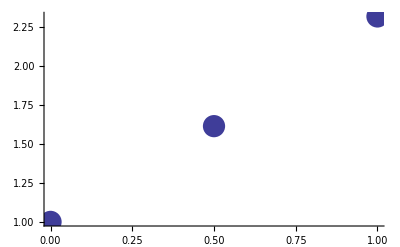

-2. (1-x) (-0.5+x)-6.4604 (-1+x) x+4.6394 (-0.5+x) x

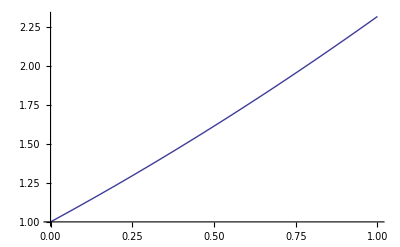

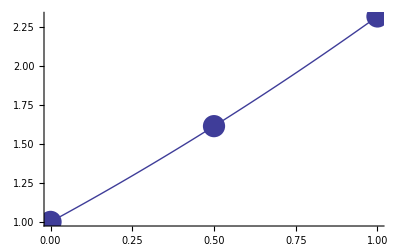

```mathematica
n= Input["dame el grado del polinomio"];
matrizx={};
matrizy={};
For[i=1, i≤n+1, i++,

variablex= Input["dame la x"<>ToString[i]];
AppendTo[matrizx, variablex];
variabley =Input["dame la y"<>ToString[i]];
AppendTo[matrizy, variabley]
]

matrizx ;
matrizy;
experimento=Table[{matrizx[[i]], matrizy[[i]]}, {i, 1, n+1}];
grafica1=ListPlot[experimento, PlotStyle->PointSize[0.04],PlotRange->All]


suma=0;
For[i=1,i≤n+1,i++,

producto= 1;
For[j=1,j≤n+1,j++,
If[j≠i,
producto=producto*(x-matrizx[[j]])/(matrizx[[i]]-matrizx[[j]]),producto]
];
suma=suma+producto*matrizy[[i]]
]
p[x_]=suma
Grafica2=Plot[p[x],{x,matrizx[[1]],matrizx[[n+1]]}]
Show[grafica1,Grafica2]
```

1.95621

1.97712

0.0105723

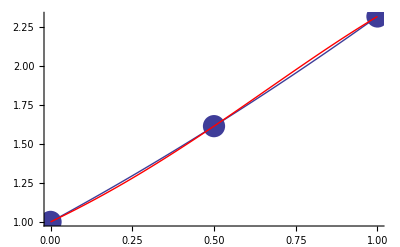

```mathematica
est=p[0.75]
real=Exp[Sin[0.75]]
error=Abs[(real-est)/real]
Show[grafica1,Grafica2, Plot[Exp[Sin[x]], {x, 0, 1}, PlotStyle->Red]]
```